```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=4;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

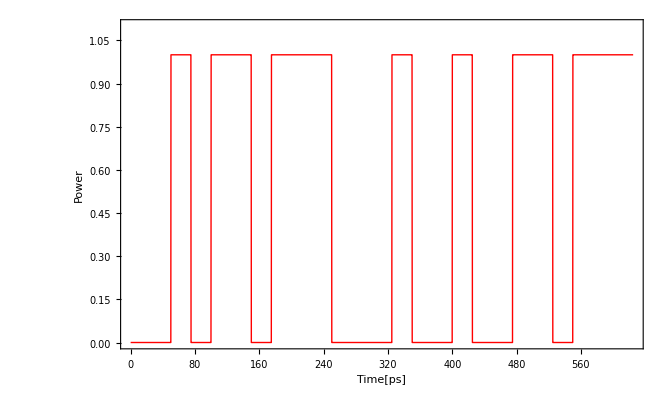

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->30},PlotRange->{0,1.1}]
```

1/2 (1+Cos[400000000000000 π t])

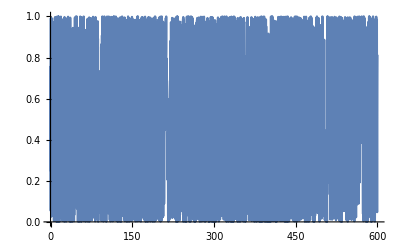

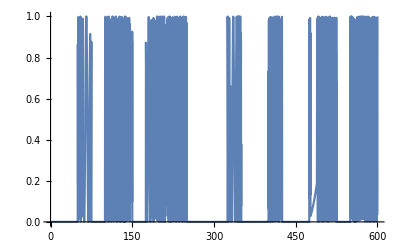

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t_]= (Cos[2*Pi*Fc*t]+1)/2
Plot[carrier[t], {t,0,600}]
cs[t_]:=signal[t]*carrier[t]
Plot[cs[t*10^-12],{t,0,600}]
```

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-(ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π)

```mathematica
fc[f_]:=-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))
```

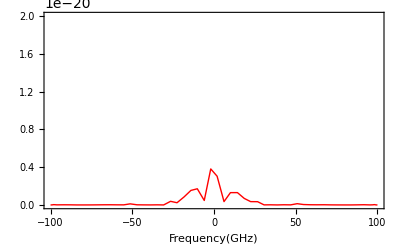

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

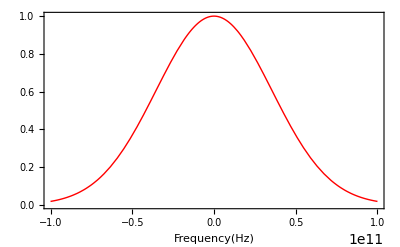

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

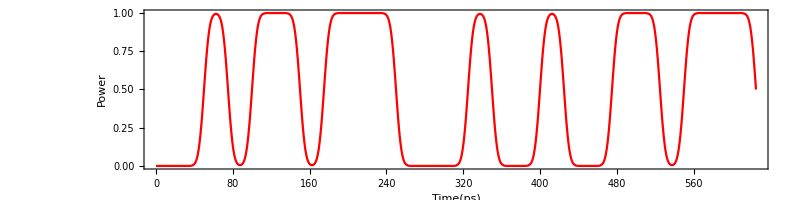

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

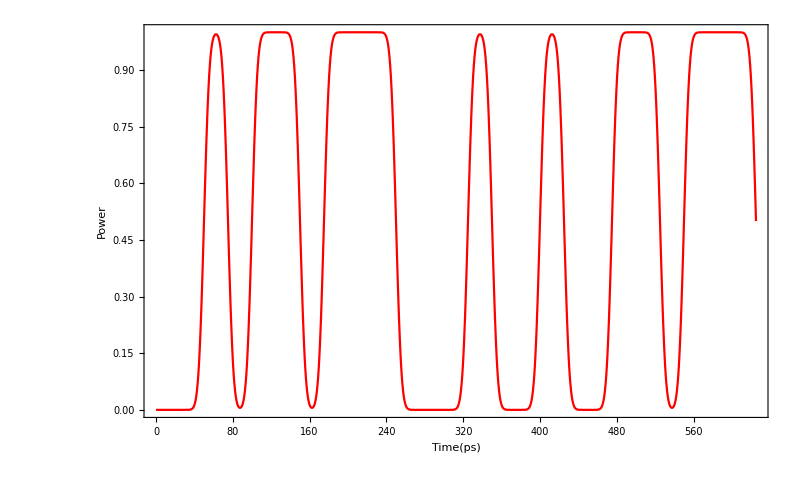

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->40,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
f[x_]:=1/(√(2*Pi*β2*L))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*L)-Pi/4)];
```

```mathematica
FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]
```

{4.41712×10^16,{x1→3.17201}}

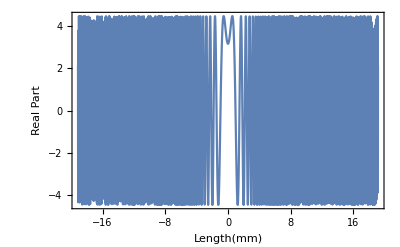

```mathematica
max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]
```

## Impulse Responce for Fiber Dispersion

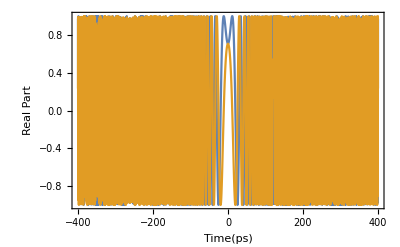

```mathematica
hdis[t_]:=(*1/(√(2*Pi*β2*L))*10^6**)Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
hcmp[t_]:=
(*1/(√(2*Pi*β2*80))*10^6*)Exp[+ⅈ*(t^2/(2*β2*L)-Pi/4)];
```

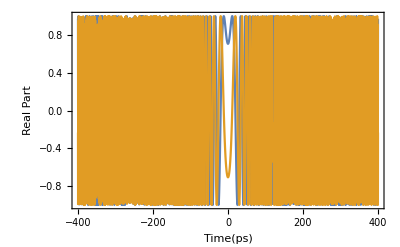

```mathematica
Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]
```

```mathematica
IntegerPart[total*10^12]
```

784

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

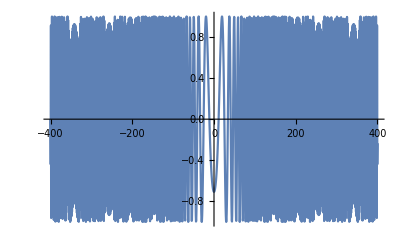

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

## Simulation

```mathematica
simu0[a_]:=simu0[a]=Sum[hdis2[z]*hcmp3[a-z],{z,-10000,10000,samp}]
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*simu0[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

12.3578-1.49743 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,12.4482},{-99.5,12.0264},{-99.,11.5824},{-98.5,11.1445},{-98.,10.6974},{-97.5,10.2483},{-97.,9.80116},{-96.5,9.35056},{-96.,8.90523},{-95.5,8.46233},{-95.,8.0244},{-94.5,7.59677},{-94.,7.17847},{-93.5,6.77771},{-93.,6.39831},{-92.5,6.04643},{-92.,5.73249},{-91.5,5.46188},{-91.,5.24443},{-90.5,5.08518},{-90.,4.98502},{-89.5,4.94324},{-89.,4.95046},{-88.5,4.9963},{-88.,5.06706},{-87.5,5.14721},{-87.,5.22458},{-86.5,5.28618},{-86.,5.32281},{-85.5,5.32784},{-85.,5.29535},{-84.5,5.22415},{-84.,5.11307},{-83.5,4.96339},{-83.,4.77887},{-82.5,4.56237},{-82.,4.3202},{-81.5,4.05809},{-81.,3.78225},{-80.5,3.50085},{-80.,3.2198},{-79.5,2.94674},{-79.,2.688},{-78.5,2.44812},{-78.,2.23213},{-77.5,2.04166},{-77.,1.87855},{-76.5,1.74463},{-76.,1.64249},{-75.5,1.57952},{-75.,1.56635},{-74.5,1.61649},{-74.,1.74122},{-73.5,1.94548},{-73.,2.22596},{-72.5,2.57482},{-72.,2.98202},{-71.5,3.43601},{-71.,3.92723},{-70.5,4.44494},{-70.,4.97977},{-69.5,5.52315},{-69.,6.06612},{-68.5,6.6015},{-68.,7.12219},{-67.5,7.62219},{-67.,8.09644},{-66.5,8.54112},{-66.,8.95308},{-65.5,9.33062},{-65.,9.67323},{-64.5,9.98069},{-64.,10.255},{-63.5,10.498},{-63.,10.7125},{-62.5,10.9024},{-62.,11.0707},{-61.5,11.2213},{-61.,11.3572},{-60.5,11.4809},{-60.,11.5943},{-59.5,11.6987},{-59.,11.7941},{-58.5,11.8803},{-58.,11.957},{-57.5,12.0227},{-57.,12.0772},{-56.5,12.1199},{-56.,12.1508},{-55.5,12.1707},{-55.,12.1811},{-54.5,12.1839},{-54.,12.1821},{-53.5,12.1794},{-53.,12.1794},{-52.5,12.1871},{-52.,12.2069},{-51.5,12.2431},{-51.,12.3001},{-50.5,12.3815},{-50.,12.4901},{-49.5,12.628},{-49.,12.7967},{-48.5,12.9964},{-48.,13.2275},{-47.5,13.4894},{-47.,13.7814},{-46.5,14.1029},{-46.,14.4531},{-45.5,14.8312},{-45.,15.2362},{-44.5,15.6671},{-44.,16.1219},{-43.5,16.5989},{-43.,17.0951},{-42.5,17.6072},{-42.,18.1312},{-41.5,18.6624},{-41.,19.1955},{-40.5,19.7251},{-40.,20.2455},{-39.5,20.7507},{-39.,21.2354},{-38.5,21.6939},{-38.,22.1214},{-37.5,22.5136},{-37.,22.8672},{-36.5,23.1793},{-36.,23.4488},{-35.5,23.6759},{-35.,23.8617},{-34.5,24.0096},{-34.,24.1241},{-33.5,24.211},{-33.,24.2777},{-32.5,24.3325},{-32.,24.3837},{-31.5,24.4399},{-31.,24.5094},{-30.5,24.5984},{-30.,24.7122},{-29.5,24.8538},{-29.,25.0237},{-28.5,25.2201},{-28.,25.4398},{-27.5,25.677},{-27.,25.9252},{-26.5,26.1773},{-26.,26.4259},{-25.5,26.6641},{-25.,26.886},{-24.5,27.0869},{-24.,27.2631},{-23.5,27.4128},{-23.,27.5348},{-22.5,27.6295},{-22.,27.6974},{-21.5,27.7396},{-21.,27.7568},{-20.5,27.7495},{-20.,27.7173},{-19.5,27.6591},{-19.,27.5725},{-18.5,27.4549},{-18.,27.3027},{-17.5,27.1121},{-17.,26.8796},{-16.5,26.6018},{-16.,26.2763},{-15.5,25.9013},{-15.,25.4764},{-14.5,25.0016},{-14.,24.4783},{-13.5,23.9087},{-13.,23.2953},{-12.5,22.6409},{-12.,21.9491},{-11.5,21.2228},{-11.,20.4653},{-10.5,19.6796},{-10.,18.8685},{-9.5,18.0345},{-9.,17.1802},{-8.5,16.3079},{-8.,15.4195},{-7.5,14.5168},{-7.,13.6015},{-6.5,12.6745},{-6.,11.7363},{-5.5,10.7867},{-5.,9.82493},{-4.5,8.84951},{-4.,7.85872},{-3.5,6.85094},{-3.,5.82526},{-2.5,4.78362},{-2.,3.73421},{-1.5,2.70407},{-1.,1.78969},{-0.5,1.35893},{0.,1.86114},{0.5,2.87212},{1.,4.0437},{1.5,5.27786},{2.,6.54018},{2.5,7.81262},{3.,9.08298},{3.5,10.3415},{4.,11.5804},{4.5,12.7931},{5.,13.9743},{5.5,15.1196},{6.,16.2256},{6.5,17.2891},{7.,18.3073},{7.5,19.2775},{8.,20.1965},{8.5,21.0608},{9.,21.8665},{9.5,22.6094},{10.,23.2849},{10.5,23.8885},{11.,24.4163},{11.5,24.8645},{12.,25.2308},{12.5,25.5137},{13.,25.7133},{13.5,25.8307},{14.,25.8686},{14.5,25.8304},{15.,25.7203},{15.5,25.5428},{16.,25.3022},{16.5,25.0024},{17.,24.6466},{17.5,24.2372},{18.,23.7759},{18.5,23.2637},{19.,22.7018},{19.5,22.0911},{20.,21.4339},{20.5,20.7333},{21.,19.9941},{21.5,19.2227},{22.,18.4269},{22.5,17.6157},{23.,16.7987},{23.5,15.9855},{24.,15.185},{24.5,14.4041},{25.,13.6486},{25.5,12.9217},{26.,12.2247},{26.5,11.5571},{27.,10.9175},{27.5,10.3041},{28.,9.71503},{28.5,9.14954},{29.,8.60813},{29.5,8.09222},{30.,7.60438},{30.5,7.14757},{31.,6.72477},{31.5,6.33755},{32.,5.98583},{32.5,5.66692},{33.,5.37513},{33.5,5.10151},{34.,4.83497},{34.5,4.56436},{35.,4.28378},{35.5,4.00506},{36.,3.78506},{36.5,3.77061},{37.,4.21656},{37.5,5.37909},{38.,7.40158},{38.5,10.3795},{39.,14.4523},{39.5,19.8267},{40.,26.7738},{40.5,35.6232},{41.,46.7581},{41.5,60.609},{42.,77.6446},{42.5,98.3592},{43.,123.256},{43.5,152.829},{44.,187.535},{44.5,227.774},{45.,273.859},{45.5,325.994},{46.,384.248},{46.5,448.54},{47.,518.623},{47.5,594.082},{48.,674.335},{48.5,758.64},{49.,846.122},{49.5,935.791},{50.,1026.58},{50.5,1117.38},{51.,1207.08},{51.5,1294.61},{52.,1378.97},{52.5,1459.28},{53.,1534.77},{53.5,1604.87},{54.,1669.14},{54.5,1727.34},{55.,1779.37},{55.5,1825.3},{56.,1865.34},{56.5,1899.8},{57.,1929.09},{57.5,1953.66},{58.,1974.},{58.5,1990.61},{59.,2003.98},{59.5,2014.55},{60.,2022.73},{60.5,2028.87},{61.,2033.26},{61.5,2036.14},{62.,2037.66},{62.5,2037.92},{63.,2036.96},{63.5,2034.74},{64.,2031.16},{64.5,2026.07},{65.,2019.24},{65.5,2010.37},{66.,1999.13},{66.5,1985.11},{67.,1967.86},{67.5,1946.9},{68.,1921.74},{68.5,1891.9},{69.,1856.91},{69.5,1816.38},{70.,1769.98},{70.5,1717.52},{71.,1658.92},{71.5,1594.26},{72.,1523.79},{72.5,1447.92},{73.,1367.25},{73.5,1282.52},{74.,1194.6},{74.5,1104.51},{75.,1013.31},{75.5,922.106},{76.,832.021},{76.5,744.122},{77.,659.403},{77.5,578.746},{78.,502.896},{78.5,432.438},{79.,367.791},{79.5,309.201},{80.,256.749},{80.5,210.365},{81.,169.846},{81.5,134.879},{82.,105.07},{82.5,79.9715},{83.,59.1087},{83.5,42.0143},{84.,28.2656},{84.5,17.5658},{85.,10.0153},{85.5,6.87273},{86.,8.29061},{86.5,10.7372},{87.,12.5569},{87.5,13.4123},{88.,13.2318},{88.5,12.0049},{89.,9.82793},{89.5,7.37947},{90.,7.66622},{90.5,13.422},{91.,23.1049},{91.5,36.0565},{92.,52.4422},{92.5,72.6505},{93.,97.1389},{93.5,126.377},{94.,160.811},{94.5,200.834},{95.,246.754},{95.5,298.77},{96.,356.95},{96.5,421.206},{97.,491.287},{97.5,566.768},{98.,647.061},{98.5,731.415},{99.,818.947},{99.5,908.662},{100.,999.488},{100.5,1090.31},{101.,1180.03},{101.5,1267.56},{102.,1351.92},{102.5,1432.23},{103.,1507.73},{103.5,1577.85},{104.,1642.17},{104.5,1700.42},{105.,1752.55},{105.5,1798.6},{106.,1838.8},{106.5,1873.45},{107.,1902.96},{107.5,1927.8},{108.,1948.47},{108.5,1965.46},{109.,1979.3},{109.5,1990.44},{110.,1999.33},{110.5,2006.37},{111.,2011.89},{111.5,2016.19},{112.,2019.53},{112.5,2022.11},{113.,2024.1},{113.5,2025.63},{114.,2026.82},{114.5,2027.76},{115.,2028.51},{115.5,2029.13},{116.,2029.68},{116.5,2030.17},{117.,2030.64},{117.5,2031.1},{118.,2031.57},{118.5,2032.04},{119.,2032.52},{119.5,2033.},{120.,2033.48},{120.5,2033.96},{121.,2034.43},{121.5,2034.91},{122.,2035.37},{122.5,2035.84},{123.,2036.32},{123.5,2036.81},{124.,2037.31},{124.5,2037.84},{125.,2038.4},{125.5,2038.97},{126.,2039.56},{126.5,2040.16},{127.,2040.76},{127.5,2041.34},{128.,2041.91},{128.5,2042.44},{129.,2042.94},{129.5,2043.39},{130.,2043.79},{130.5,2044.16},{131.,2044.48},{131.5,2044.77},{132.,2045.03},{132.5,2045.25},{133.,2045.44},{133.5,2045.6},{134.,2045.69},{134.5,2045.71},{135.,2045.62},{135.5,2045.36},{136.,2044.9},{136.5,2044.16},{137.,2043.04},{137.5,2041.43},{138.,2039.2},{138.5,2036.17},{139.,2032.13},{139.5,2026.83},{140.,2019.98},{140.5,2011.22},{141.,2000.15},{141.5,1986.35},{142.,1969.33},{142.5,1948.59},{143.,1923.63},{143.5,1893.94},{144.,1859.06},{144.5,1818.59},{145.,1772.22},{145.5,1719.74},{146.,1661.09},{146.5,1596.35},{147.,1525.77},{147.5,1449.78},{148.,1368.96},{148.5,1284.07},{149.,1195.98},{149.5,1105.69},{150.,1014.29},{150.5,922.877},{151.,832.574},{151.5,744.456},{152.,659.521},{152.5,578.657},{153.,502.616},{153.5,431.989},{154.,367.201},{154.5,308.503},{155.,255.98},{155.5,209.563},{156.,169.048},{156.5,134.121},{157.,104.382},{157.5,79.3779},{158.,58.626},{158.5,41.649},{159.,28.0108},{159.5,17.3909},{160.,9.83088},{160.5,6.51047},{161.,7.80293},{161.5,10.2019},{162.,11.9916},{162.5,12.8336},{163.,12.6586},{163.5,11.4552},{164.,9.31841},{164.5,6.94702},{165.,7.44304},{165.5,13.3164},{166.,22.9652},{166.5,35.8292},{167.,52.1101},{167.5,72.2121},{168.,96.6023},{168.5,125.758},{169.,160.13},{169.5,200.116},{170.,246.029},{170.5,298.07},{171.,356.306},{171.5,420.65},{172.,490.849},{172.5,566.476},{173.,646.937},{173.5,731.48},{174.,819.215},{174.5,909.143},{175.,1000.19},{175.5,1091.23},{176.,1181.16},{176.5,1268.9},{177.,1353.46},{177.5,1433.94},{178.,1509.6},{178.5,1579.85},{179.,1644.27},{179.5,1702.59},{180.,1754.74},{180.5,1800.78},{181.,1840.92},{181.5,1875.46},{182.,1904.82},{182.5,1929.45},{183.,1949.87},{183.5,1966.57},{184.,1980.08},{184.5,1990.87},{185.,1999.38},{185.5,2006.03},{186.,2011.16},{186.5,2015.07},{187.,2018.03},{187.5,2020.25},{188.,2021.89},{188.5,2023.11},{189.,2023.99},{189.5,2024.65},{190.,2025.13},{190.5,2025.5},{191.,2025.78},{191.5,2026.02},{192.,2026.22},{192.5,2026.39},{193.,2026.55},{193.5,2026.68},{194.,2026.79},{194.5,2026.86},{195.,2026.9},{195.5,2026.89},{196.,2026.84},{196.5,2026.74},{197.,2026.6},{197.5,2026.42},{198.,2026.2},{198.5,2025.97},{199.,2025.73},{199.5,2025.5},{200.,2025.27},{200.5,2025.06},{201.,2024.88},{201.5,2024.72},{202.,2024.58},{202.5,2024.47},{203.,2024.38},{203.5,2024.31},{204.,2024.25},{204.5,2024.21},{205.,2024.18},{205.5,2024.17},{206.,2024.18},{206.5,2024.23},{207.,2024.31},{207.5,2024.42},{208.,2024.59},{208.5,2024.79},{209.,2025.04},{209.5,2025.34},{210.,2025.67},{210.5,2026.03},{211.,2026.41},{211.5,2026.8},{212.,2027.21},{212.5,2027.61},{213.,2028.02},{213.5,2028.42},{214.,2028.81},{214.5,2029.21},{215.,2029.61},{215.5,2030.02},{216.,2030.45},{216.5,2030.88},{217.,2031.32},{217.5,2031.78},{218.,2032.24},{218.5,2032.71},{219.,2033.16},{219.5,2033.61},{220.,2034.05},{220.5,2034.46},{221.,2034.85},{221.5,2035.23},{222.,2035.59},{222.5,2035.93},{223.,2036.28},{223.5,2036.62},{224.,2036.97},{224.5,2037.34},{225.,2037.72},{225.5,2038.12},{226.,2038.53},{226.5,2038.94},{227.,2039.37},{227.5,2039.78},{228.,2040.2},{228.5,2040.6},{229.,2040.98},{229.5,2041.36},{230.,2041.72},{230.5,2042.08},{231.,2042.45},{231.5,2042.81},{232.,2043.19},{232.5,2043.58},{233.,2043.97},{233.5,2044.35},{234.,2044.71},{234.5,2045.01},{235.,2045.22},{235.5,2045.3},{236.,2045.18},{236.5,2044.8},{237.,2044.05},{237.5,2042.82},{238.,2040.99},{238.5,2038.36},{239.,2034.74},{239.5,2029.87},{240.,2023.45},{240.5,2015.13},{241.,2004.52},{241.5,1991.17},{242.,1974.61},{242.5,1954.32},{243.,1929.8},{243.5,1900.55},{244.,1866.1},{244.5,1826.06},{245.,1780.09},{245.5,1728.01},{246.,1669.75},{246.5,1605.38},{247.,1535.18},{247.5,1459.56},{248.,1379.11},{248.5,1294.59},{249.,1206.88},{249.5,1116.98},{250.,1025.97},{250.5,934.952},{251.,845.046},{251.5,757.323},{252.,672.779},{252.5,592.302},{253.,516.641},{253.5,446.387},{254.,381.967},{254.5,323.632},{255.,271.472},{255.5,225.418},{256.,185.269},{256.5,150.709},{257.,121.334},{257.5,96.6787},{258.,76.2421},{258.5,59.5101},{259.,45.9766},{259.5,35.1602},{260.,26.6162},{260.5,19.9444},{261.,14.794},{261.5,10.8637},{262.,7.89986},{262.5,5.69246},{263.,4.07046},{263.5,2.8961},{264.,2.05964},{264.5,1.47443},{265.,1.07263},{265.5,0.801193},{266.,0.618438},{266.5,0.491692},{267.,0.396451},{267.5,0.316247},{268.,0.24233},{268.5,0.173286},{269.,0.116243},{269.5,0.0907756},{270.,0.105949},{270.5,0.133052},{271.,0.150652},{271.5,0.151589},{272.,0.135392},{272.5,0.106452},{273.,0.076429},{273.5,0.0703299},{274.,0.0968314},{274.5,0.130993},{275.,0.15707},{275.5,0.16869},{276.,0.163855},{276.5,0.143622},{277.,0.111565},{277.5,0.0734047},{278.,0.0382899},{278.5,0.0294337},{279.,0.0468348},{279.5,0.0590782},{280.,0.0585884},{280.5,0.044967},{281.,0.0205873},{281.5,0.0115774},{282.,0.0447175},{282.5,0.0751464},{283.,0.0981495},{283.5,0.110515},{284.,0.110718},{284.5,0.0990799},{285.,0.077704},{285.5,0.0501377},{286.,0.0207771},{286.5,0.00586439},{287.,0.0257091},{287.5,0.0358356},{288.,0.0347844},{288.5,0.0229339},{289.,0.00503173},{289.5,0.0256955},{290.,0.0536386},{290.5,0.078955},{291.,0.0976205},{291.5,0.10674},{292.,0.10491},{292.5,0.0924093},{293.,0.0711384},{293.5,0.0443435},{294.,0.0161423},{294.5,0.00921572},{295.,0.0276837},{295.5,0.0365127},{296.,0.0342649},{296.5,0.0212022},{297.,0.00189264},{297.5,0.0284585},{298.,0.057314},{298.5,0.0830839},{299.,0.101767},{299.5,0.110392},{300.,0.107475},{300.5,0.0933249},{301.,0.0700435},{301.5,0.0411968},{302.,0.0112566},{302.5,0.0150853},{303.,0.033493},{303.5,0.0407417},{304.,0.0351578},{304.5,0.0168942},{305.,0.0122853},{305.5,0.0492031},{306.,0.0904441},{306.5,0.132971},{307.,0.175373},{307.5,0.219076},{308.,0.269576},{308.5,0.337575},{309.,0.440041},{309.5,0.601313},{310.,0.85437},{310.5,1.2424},{311.,1.8208},{311.5,2.65984},{312.,3.84805},{312.5,5.49648},{313.,7.74361},{313.5,10.7607},{314.,14.7573},{314.5,19.986},{315.,26.7463},{315.5,35.3867},{316.,46.3035},{316.5,59.9373},{317.,76.7644},{317.5,97.2855},{318.,122.009},{318.5,151.431},{319.,186.011},{319.5,226.151},{320.,272.162},{320.5,324.248},{321.,382.475},{321.5,446.76},{322.,516.852},{322.5,592.332},{323.,672.614},{323.5,756.954},{324.,844.471},{324.5,934.175},{325.,1024.99},{325.5,1115.82},{326.,1205.54},{326.5,1293.09},{327.,1377.46},{327.5,1457.77},{328.,1533.28},{328.5,1603.39},{329.,1667.67},{329.5,1725.89},{330.,1777.95},{330.5,1823.92},{331.,1864.02},{331.5,1898.55},{332.,1927.92},{332.5,1952.6},{333.,1973.07},{333.5,1989.82},{334.,2003.35},{334.5,2014.11},{335.,2022.5},{335.5,2028.87},{336.,2033.53},{336.5,2036.69},{337.,2038.52},{337.5,2039.12},{338.,2038.52},{338.5,2036.69},{339.,2033.53},{339.5,2028.88},{340.,2022.5},{340.5,2014.11},{341.,2003.35},{341.5,1989.82},{342.,1973.07},{342.5,1952.6},{343.,1927.92},{343.5,1898.55},{344.,1864.01},{344.5,1823.92},{345.,1777.94},{345.5,1725.88},{346.,1667.67},{346.5,1603.39},{347.,1533.28},{347.5,1457.78},{348.,1377.47},{348.5,1293.09},{349.,1205.55},{349.5,1115.83},{350.,1025.},{350.5,934.175},{351.,844.47},{351.5,756.951},{352.,672.61},{352.5,592.327},{353.,516.846},{353.5,446.755},{354.,382.472},{354.5,324.247},{355.,272.163},{355.5,226.154},{356.,186.017},{356.5,151.438},{357.,122.017},{357.5,97.2929},{358.,76.7702},{358.5,59.9405},{359.,46.3037},{359.5,35.3836},{360.,26.7403},{360.5,19.9778},{361.,14.748},{361.5,10.7516},{362.,7.73618},{362.5,5.49198},{363.,3.8474},{363.5,2.66347},{364.,1.8285},{364.5,1.25332},{365.,0.867127},{365.5,0.614216},{366.,0.451251},{366.5,0.345336},{367.,0.272529},{367.5,0.216532},{368.,0.167442},{368.5,0.120574},{369.,0.0752487},{369.5,0.0334204},{370.,0.00166525},{370.5,0.0266049},{371.,0.038808},{371.5,0.0372442},{372.,0.0228276},{372.5,0.0016929},{373.,0.032069},{373.5,0.0632444},{374.,0.0900368},{374.5,0.10807},{375.,0.114439},{375.5,0.108096},{376.,0.0900389},{376.5,0.0632157},{377.,0.0320262},{377.5,0.00158087},{378.,0.0230493},{378.5,0.0375828},{379.,0.0392419},{379.5,0.0271626},{380.,0.00261304},{380.5,0.0327974},{381.,0.0746841},{381.5,0.120118},{382.,0.167186},{382.5,0.216619},{383.,0.27304},{383.5,0.346282},{384.,0.452648},{384.5,0.61604},{385.,0.869224},{385.5,1.25546},{386.,1.83049},{386.5,2.66504},{387.,3.84824},{387.5,5.49179},{388.,7.73476},{388.5,10.7488},{389.,14.7438},{389.5,19.9724},{390.,26.7342},{390.5,35.3773},{391.,46.2978},{391.5,59.9359},{392.,76.7676},{392.5,97.2931},{393.,122.02},{393.5,151.445},{394.,186.028},{394.5,226.169},{395.,272.181},{395.5,324.265},{396.,382.49},{396.5,446.77},{397.,516.856},{397.5,592.329},{398.,672.603},{398.5,756.934},{399.,844.443},{399.5,934.138},{400.,1024.95},{400.5,1115.77},{401.,1205.5},{401.5,1293.05},{402.,1377.43},{402.5,1457.75},{403.,1533.28},{403.5,1603.4},{404.,1667.71},{404.5,1725.95},{405.,1778.04},{405.5,1824.03},{406.,1864.14},{406.5,1898.68},{407.,1928.06},{407.5,1952.72},{408.,1973.16},{408.5,1989.88},{409.,2003.37},{409.5,2014.07},{410.,2022.4},{410.5,2028.72},{411.,2033.32},{411.5,2036.43},{412.,2038.23},{412.5,2038.8},{413.,2038.19},{413.5,2036.36},{414.,2033.23},{414.5,2028.61},{415.,2022.3},{415.5,2013.98},{416.,2003.31},{416.5,1989.88},{417.,1973.22},{417.5,1952.87},{418.,1928.3},{418.5,1899.03},{419.,1864.6},{419.5,1824.59},{420.,1778.69},{420.5,1726.69},{421.,1668.52},{421.5,1604.25},{422.,1534.14},{422.5,1458.6},{423.,1378.23},{423.5,1293.76},{424.,1206.1},{424.5,1116.23},{425.,1025.23},{425.5,934.202},{426.,844.273},{426.5,756.511},{427.,671.913},{427.5,591.363},{428.,515.611},{428.5,445.25},{429.,380.706},{429.5,322.233},{430.,269.922},{430.5,223.711},{431.,183.402},{431.5,148.686},{432.,119.168},{432.5,94.3884},{433.,73.8557},{433.5,57.0642},{434.,43.5176},{434.5,32.7449},{435.,24.3147},{435.5,17.845},{436.,13.0105},{436.5,9.54536},{437.,7.23355},{437.5,5.87277},{438.,5.22362},{438.5,5.018},{439.,5.03676},{439.5,5.1516},{440.,5.30524},{440.5,5.478},{441.,5.66539},{441.5,5.86744},{442.,6.0847},{442.5,6.31726},{443.,6.56532},{443.5,6.82977},{444.,7.11239},{444.5,7.41596},{445.,7.74398},{445.5,8.09999},{446.,8.48712},{446.5,8.90748},{447.,9.36155},{447.5,9.848},{448.,10.3638},{448.5,10.9044},{449.,11.4643},{449.5,12.0382},{450.,12.6212},{450.5,13.2096},{451.,13.8013},{451.5,14.3958},{452.,14.9937},{452.5,15.5963},{453.,16.2049},{453.5,16.8196},{454.,17.4392},{454.5,18.0599},{455.,18.6762},{455.5,19.2805},{456.,19.8643},{456.5,20.4195},{457.,20.9396},{457.5,21.4211},{458.,21.8659},{458.5,22.2817},{459.,22.6839},{459.5,23.0969},{460.,23.5546},{460.5,24.102},{461.,24.7972},{461.5,25.7129},{462.,26.94},{462.5,28.5913},{463.,30.8062},{463.5,33.756},{464.,37.6496},{464.5,42.7385},{465.,49.3212},{465.5,57.7445},{466.,68.4039},{466.5,81.7388},{467.,98.2249},{467.5,118.363},{468.,142.66},{468.5,171.614},{469.,205.685},{469.5,245.274},{470.,290.694},{470.5,342.149},{471.,399.706},{471.5,463.281},{472.,532.625},{472.5,607.319},{473.,686.778},{473.5,770.261},{474.,856.892},{474.5,945.684},{475.,1035.58},{475.5,1125.47},{476.,1214.25},{476.5,1300.87},{477.,1384.33},{477.5,1463.77},{478.,1538.43},{478.5,1607.74},{479.,1671.27},{479.5,1728.78},{480.,1780.19},{480.5,1825.56},{481.,1865.1},{481.5,1899.12},{482.,1928.03},{482.5,1952.3},{483.,1972.4},{483.5,1988.87},{484.,2002.19},{484.5,2012.84},{485.,2021.26},{485.5,2027.84},{486.,2032.93},{486.5,2036.82},{487.,2039.77},{487.5,2041.98},{488.,2043.62},{488.5,2044.84},{489.,2045.75},{489.5,2046.44},{490.,2046.98},{490.5,2047.44},{491.,2047.86},{491.5,2048.28},{492.,2048.73},{492.5,2049.22},{493.,2049.75},{493.5,2050.34},{494.,2050.98},{494.5,2051.66},{495.,2052.37},{495.5,2053.1},{496.,2053.84},{496.5,2054.59},{497.,2055.34},{497.5,2056.09},{498.,2056.83},{498.5,2057.57},{499.,2058.3},{499.5,2059.04},{500.,2059.76},{500.5,2060.49},{501.,2061.2},{501.5,2061.89},{502.,2062.56},{502.5,2063.2},{503.,2063.79},{503.5,2064.35},{504.,2064.85},{504.5,2065.32},{505.,2065.74},{505.5,2066.12},{506.,2066.49},{506.5,2066.83},{507.,2067.17},{507.5,2067.5},{508.,2067.82},{508.5,2068.13},{509.,2068.42},{509.5,2068.65},{510.,2068.79},{510.5,2068.8},{511.,2068.61},{511.5,2068.15},{512.,2067.33},{512.5,2066.02},{513.,2064.08},{513.5,2061.34},{514.,2057.57},{514.5,2052.53},{515.,2045.92},{515.5,2037.37},{516.,2026.51},{516.5,2012.88},{517.,1996.02},{517.5,1975.42},{518.,1950.58},{518.5,1921.01},{519.,1886.25},{519.5,1845.91},{520.,1799.67},{520.5,1747.34},{521.,1688.87},{521.5,1624.34},{522.,1554.01},{522.5,1478.31},{523.,1397.83},{523.5,1313.33},{524.,1225.69},{524.5,1135.91},{525.,1045.06},{525.5,954.249},{526.,864.597},{526.5,777.172},{527.,692.964},{527.5,612.856},{528.,537.588},{528.5,467.745},{529.,403.742},{529.5,345.821},{530.,294.057},{530.5,248.373},{531.,208.558},{531.5,174.289},{532.,145.158},{532.5,120.701},{533.,100.422},{533.5,83.8202},{534.,70.406},{534.5,59.7231},{535.,51.3589},{535.5,44.9547},{536.,40.2114},{536.5,36.8944},{537.,34.8359},{537.5,33.9366},{538.,34.1678},{538.5,35.5714},{539.,38.2595},{539.5,42.4121},{540.,48.2747},{540.5,56.1537},{541.,66.4121},{541.5,79.4629},{542.,95.7603},{542.5,115.787},{543.,140.037},{543.5,168.998},{544.,203.122},{544.5,242.805},{545.,288.357},{545.5,339.976},{546.,397.728},{546.5,461.523},{547.,531.108},{547.5,606.058},{548.,685.782},{548.5,769.532},{549.,856.424},{549.5,945.464},{550.,1035.58},{550.5,1125.67},{551.,1214.63},{551.5,1301.39},{552.,1384.97},{552.5,1464.48},{553.,1539.2},{553.5,1608.53},{554.,1672.06},{554.5,1729.55},{555.,1780.92},{555.5,1826.24},{556.,1865.71},{556.5,1899.66},{557.,1928.49},{557.5,1952.66},{558.,1972.68},{558.5,1989.05},{559.,2002.27},{559.5,2012.83},{560.,2021.17},{560.5,2027.67},{561.,2032.7},{561.5,2036.54},{562.,2039.46},{562.5,2041.66},{563.,2043.31},{563.5,2044.55},{564.,2045.5},{564.5,2046.23},{565.,2046.83},{565.5,2047.35},{566.,2047.83},{566.5,2048.3},{567.,2048.79},{567.5,2049.31},{568.,2049.87},{568.5,2050.47},{569.,2051.11},{569.5,2051.78},{570.,2052.48},{570.5,2053.19},{571.,2053.92},{571.5,2054.64},{572.,2055.37},{572.5,2056.09},{573.,2056.81},{573.5,2057.53},{574.,2058.25},{574.5,2058.96},{575.,2059.68},{575.5,2060.4},{576.,2061.11},{576.5,2061.8},{577.,2062.49},{577.5,2063.14},{578.,2063.77},{578.5,2064.36},{579.,2064.91},{579.5,2065.41},{580.,2065.87},{580.5,2066.29},{581.,2066.68},{581.5,2067.05},{582.,2067.4},{582.5,2067.74},{583.,2068.08},{583.5,2068.42},{584.,2068.77},{584.5,2069.13},{585.,2069.5},{585.5,2069.87},{586.,2070.23},{586.5,2070.58},{587.,2070.92},{587.5,2071.23},{588.,2071.52},{588.5,2071.78},{589.,2072.01},{589.5,2072.21},{590.,2072.39},{590.5,2072.54},{591.,2072.66},{591.5,2072.77},{592.,2072.84},{592.5,2072.89},{593.,2072.91},{593.5,2072.89},{594.,2072.84},{594.5,2072.74},{595.,2072.6},{595.5,2072.42},{596.,2072.2},{596.5,2071.95},{597.,2071.67},{597.5,2071.39},{598.,2071.1},{598.5,2070.82},{599.,2070.56},{599.5,2070.33},{600.,2070.13},{600.5,2069.97},{601.,2069.83},{601.5,2069.73},{602.,2069.65},{602.5,2069.58},{603.,2069.52},{603.5,2069.48},{604.,2069.43},{604.5,2069.39},{605.,2069.36},{605.5,2069.34},{606.,2069.34},{606.5,2069.36},{607.,2069.4},{607.5,2069.47},{608.,2069.54},{608.5,2069.62},{609.,2069.67},{609.5,2069.67},{610.,2069.57},{610.5,2069.32},{611.,2068.87},{611.5,2068.12},{612.,2067.},{612.5,2065.38},{613.,2063.12},{613.5,2060.06},{614.,2055.99},{614.5,2050.66},{615.,2043.78},{615.5,2035.},{616.,2023.94},{616.5,2010.17},{617.,1993.2},{617.5,1972.55},{618.,1947.71},{618.5,1918.18},{619.,1883.51},{619.5,1843.3},{620.,1797.23},{620.5,1745.11},{621.,1686.86},{621.5,1622.58},{622.,1552.51},{622.5,1477.08},{623.,1396.87},{623.5,1312.64},{624.,1225.27},{624.5,1135.73},{625.,1045.11},{625.5,954.511},{626.,865.033},{626.5,777.745},{627.,693.637},{627.5,613.588},{628.,538.341},{628.5,468.484},{629.,404.436},{629.5,346.448},{630.,294.603},{630.5,248.833},{631.,208.933},{631.5,174.588},{632.,145.392},{632.5,120.879},{633.,100.548},{633.5,83.8802},{634.,70.3686},{634.5,59.5274},{635.,50.9076},{635.5,44.1052},{636.,38.7668},{636.5,34.5906},{637.,31.3256},{637.5,28.7673},{638.,26.7526},{638.5,25.1524},{639.,23.866},{639.5,22.815},{640.,21.9385},{640.5,21.1891},{641.,20.5308},{641.5,19.9363},{642.,19.3858},{642.5,18.866},{643.,18.3691},{643.5,17.8916},{644.,17.4331},{644.5,16.9958},{645.,16.5825},{645.5,16.196},{646.,15.8379},{646.5,15.5082},{647.,15.2041},{647.5,14.9211},{648.,14.6523},{648.5,14.3894},{649.,14.1231},{649.5,13.8441},{650.,13.5433},{650.5,13.2132},{651.,12.8476},{651.5,12.4422},{652.,11.9946},{652.5,11.5046},{653.,10.9731},{653.5,10.4022},{654.,9.79527},{654.5,9.15564},{655.,8.48729},{655.5,7.79427},{656.,7.0811},{656.5,6.3529},{657.,5.61708},{657.5,4.88394},{658.,4.16988},{658.5,3.50252},{659.,2.92843},{659.5,2.52217},{660.,2.37246},{660.5,2.51596},{661.,2.89169},{661.5,3.40152},{662.,3.97001},{662.5,4.55149},{663.,5.11926},{663.5,5.65882},{664.,6.16226},{664.5,6.62662},{665.,7.05172},{665.5,7.44002},{666.,7.79441},{666.5,8.11876},{667.,8.41684},{667.5,8.6916},{668.,8.9457},{668.5,9.18096},{669.,9.39873},{669.5,9.59985},{670.,9.7861},{670.5,9.9589},{671.,10.1214},{671.5,10.2782},{672.,10.4346},{672.5,10.5983},{673.,10.7781},{673.5,10.9833},{674.,11.2237},{674.5,11.5087},{675.,11.8455},{675.5,12.2397},{676.,12.6935},{676.5,13.2057},{677.,13.7727},{677.5,14.387},{678.,15.0398},{678.5,15.7206},{679.,16.4179},{679.5,17.1204},{680.,17.817},{680.5,18.4977},{681.,19.1535},{681.5,19.7773},{682.,20.3625},{682.5,20.9048},{683.,21.4008},{683.5,21.8481},{684.,22.2459},{684.5,22.5937},{685.,22.8918},{685.5,23.1408},{686.,23.342},{686.5,23.4962},{687.,23.6045},{687.5,23.6685},{688.,23.6886},{688.5,23.6665},{689.,23.6023},{689.5,23.4967},{690.,23.3502},{690.5,23.1621},{691.,22.9321},{691.5,22.6593},{692.,22.3419},{692.5,21.9784},{693.,21.567},{693.5,21.1057},{694.,20.5932},{694.5,20.0295},{695.,19.4141},{695.5,18.7498},{696.,18.0396},{696.5,17.289},{697.,16.5063},{697.5,15.7003},{698.,14.8834},{698.5,14.0687},{699.,13.2713},{699.5,12.5069},{700.,11.7913},{700.5,11.1394},{701.,10.564},{701.5,10.0751},{702.,9.67701},{702.5,9.37064},{703.,9.15063},{703.5,9.00704},{704.,8.92845},{704.5,8.89957},{705.,8.90719},{705.5,8.93835},{706.,8.98133},{706.5,9.02768},{707.,9.06933},{707.5,9.10056},{708.,9.11655},{708.5,9.11328},{709.,9.08716},{709.5,9.03525},{710.,8.95464},{710.5,8.84223},{711.,8.69658},{711.5,8.51493},{712.,8.29667},{712.5,8.04185},{713.,7.74995},{713.5,7.42492},{714.,7.06925},{714.5,6.68953},{715.,6.29612},{715.5,5.9},{716.,5.52214},{716.5,5.18631},{717.,4.92436},{717.5,4.77509},{718.,4.77043},{718.5,4.93483},{719.,5.27016},{719.5,5.75983},{720.,6.37863},{720.5,7.09591},{721.,7.88519},{721.5,8.72284},{722.,9.58833},{722.5,10.4651},{723.,11.3379},{723.5,12.1944},{724.,13.0234},{724.5,13.8161},{725.,14.5638}}

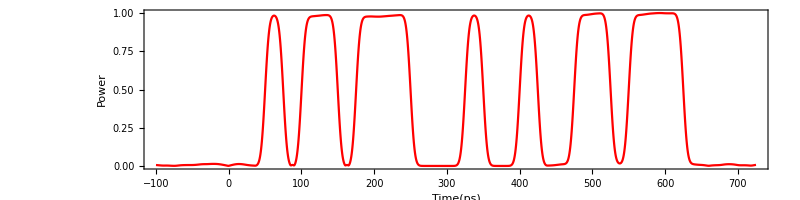

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

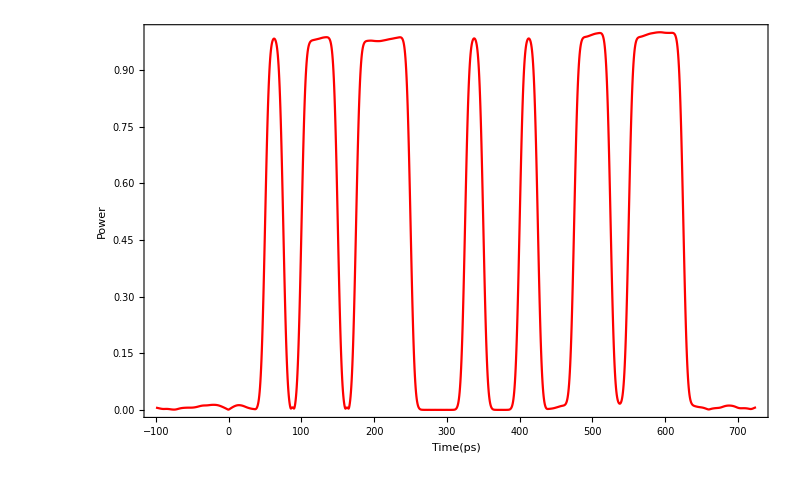

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->40,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

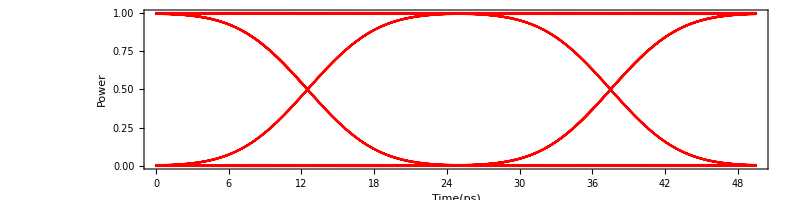

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

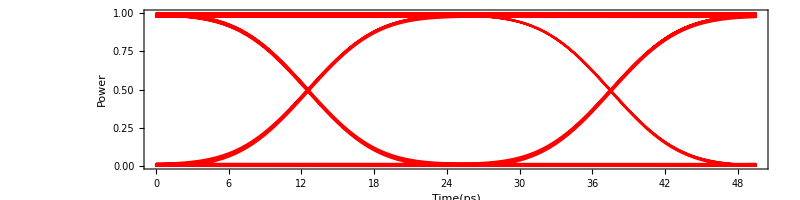

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 66 point

0 is 66 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.983919

Average of 0 is 0.00626374

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.00841801

A Standard Deviation of 0 is 0.00667701

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-9.63903×10^7]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: Exp[-9805.55]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

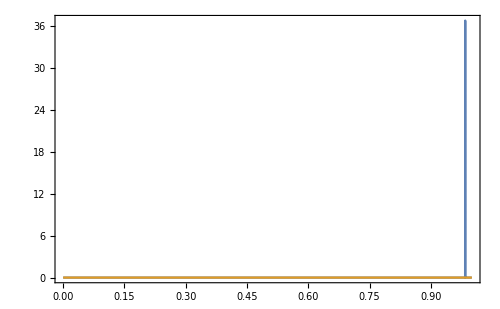

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 64.7668

Q-dB is 36.227 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.

Eye Opening is 0.98456

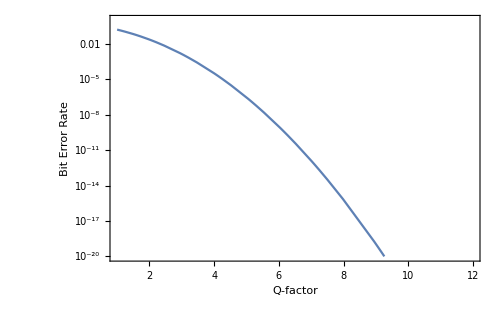

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```